```mathematica
data=Import["/Users/ayushboss/Desktop/Coding/Python/hsmc-stream-cipher-2019-git/7-12-19-3:35/stream-ciphers/python/cluster_data.csv","CSV"]
```

{{1,13.1526,26.632},{2,13.1501,26.654}}

```mathematica
clusterList={};
For[i=1,i≤ Length[data],i++,
madeCluster={data[[i]][[2]],data[[i]][[3]]};
AppendTo[clusterList, madeCluster];
];
clusterList
```

{{13.1526,26.632},{13.1501,26.654}}

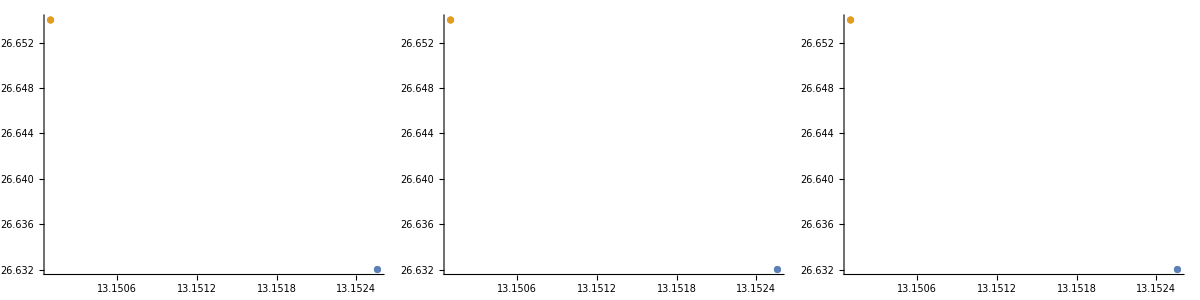

```mathematica
{{13.152560810629144,26.6319995083},{13.150097214438533,26.6539876188}}
Grid[{Table[ListPlot[FindClusters[clusterList,Method->{"NeighborhoodContraction","NeighborhoodRadius"->s}]],{s,{0.06,0.08,0.1}}]},Frame->All]
```